# On-Demand Public Transit: a Markovian Continuous Approximation Model

## Code supplement for “On-demand public transit: a Markovian continuous approximation model”

Daniel F. Silva
Alexander Vinel
Bekircan Kirkici

Department of Industrial and Systems Engineering, Auburn University
silva@auburn.edu
alexander.vinel@auburn.edu	
bekir@auburn.edu

## Section 4

## Definitions and Parameters

In this section, we first define the rate matrices for each model that we are going to use.
These matrices are generated from the formula, and its extensions, presented in the paper. 
Then we move to define required functions, thus we can start our analysis.

Below are the trip length averages are from (Vinel and Silva 2018).
Each number in M_n represents the number of passengers in the car for the  completion of the trip.

Full list of references can be found at the end of this file.

```mathematica
M1=1/(2*2/3);
M2=1/(2.230624);
M3=1/(2.882179);
```

### CTMC Models’ stationary distributions, pre-calculated imports, λ = {0.25, 0.5, 0.75, ... , 10}

We import pre-calculated using our Python code, which can be found at “https://github.com/bekirio/OnDemandPublicTransit2021”. 
We are using 40 points of λ for our graphs. These values are listed in the array named “Lambdas”. These λ values are used to get the “Generator Matrix” for the Continuous-Time Markov Chain model we proposed.

```mathematica
Lambdas = {0.25, 0.5, 0.75, 1, 1.25, 1.5, 1.75, 2, 2.25, 2.5, 2.75, 3, 3.25, 3.5, 3.75, 4, 4.25, 4.5, 4.75, 5, 5.25, 5.5, 5.75, 6, 6.25, 6.5, 6.75, 7, 7.25,7.5,7.75,8,8.25,8.5,8.75,9,9.25,9.5,9.75,10};
```

#### 1-car sDist

```mathematica
Sdist1Car3Kap1tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist1Car6Kap1tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_6DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist1Car9Kap1tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_9DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist1Car12Kap1tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_12DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist1Car3Kap2tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist1Car3Kap3tH =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 1-car indices

K = 3

```mathematica
Indices1Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices1Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {1} cannot be transposed.

{2,3,4,13}

K = 6

```mathematica
Indices1Cars6Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices1Cars6Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices1Cars6Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_6Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {1} cannot be transposed.

K = 9

```mathematica
Indices1Cars9Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices1Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices1Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {1} cannot be transposed.

K = 12

```mathematica
Indices1Cars12Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_10Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_11Wait.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices1Cars12Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices1Cars12Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_12Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {1} cannot be transposed.

tH = 2

```mathematica
Indices1Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices1Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

tH = 3

```mathematica
Indices1Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices1Cars3Kap3tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_3Wait.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {7} cannot be transposed.

```mathematica
Indices1Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices1Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","1carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

#### 2-car sDist

```mathematica
Sdist2Car3Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist2Car6Kap1tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_6DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist2Car9Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_9DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist2Car12Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_12DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist2Car3Kap2tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist2Car3Kap3tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 2-car indices

K = 3

```mathematica
Indices2Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices2Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 6

```mathematica
Indices2Cars6Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices2Cars6Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices2Cars6Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_6Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 9

```mathematica
Indices2Cars9Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices2Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices2Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 12

```mathematica
Indices2Cars12Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_10Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_11Wait.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices2Cars12Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices2Cars12Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_12Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

tH = 2

```mathematica
Indices2Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices2Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

tH = 3

```mathematica
Indices2Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices2Cars3Kap3tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_3Wait.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {13} cannot be transposed.

```mathematica
Indices2Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices2Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","2carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

#### 3-car sDist

```mathematica
Sdist3Car3Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car6Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_6DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car9Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_9DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car12Kap1tH=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_12DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist3Car6Kap2tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_6DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car9Kap2tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_9DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car12Kap2tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_12DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist3Car6Kap3tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_6DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car9Kap3tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_9DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car12Kap3tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_12DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist3Car3Kap2tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car3Kap3tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 3-car indices

K = 3, a = {1, 2, 3}

```mathematica
Indices3Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars3Kap3tH3wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_3Wait.txt"}],"Data"][[1]];
```

```mathematica
Indices3Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

K = 6, a = {1, 2, 3}

```mathematica
Indices3Cars6Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars6Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars6Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars6Kap3tH3wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_3Wait.txt"}],"Data"][[1]];
Indices3Cars6Kap3tH4wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_4Wait.txt"}],"Data"][[1]];
Indices3Cars6Kap3tH5wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_5Wait.txt"}],"Data"][[1]];
Indices3Cars6Kap3tH6wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_6Wait.txt"}],"Data"][[1]];
```

```mathematica
Indices3Cars6Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars6Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars6Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars6Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_6Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

K = 9, a = {1, 2, 3}

```mathematica
Indices3Cars9Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars9Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_6Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_7Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_9Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars9Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars9Kap3tH3wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_3Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH4wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_4Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH5wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_5Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH6wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_6Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH7wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_7Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH8wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_9Wait.txt"}],"Data"][[1]];
Indices3Cars9Kap3tH9wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_9Wait.txt"}],"Data"][[1]];
```

```mathematica
Indices3Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars9Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars9Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars9Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_9Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

K = 12, a = {1, 2, 3}

```mathematica
Indices3Cars12Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_10Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_11Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars12Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_3Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_4Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_5Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_6Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_7Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_8Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_9Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_10Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_11Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars12Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices3Cars12Kap3tH3wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_3Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH4wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_4Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH5wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_5Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH6wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_6Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH7wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_7Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH8wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_8Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH9wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_9Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH10wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_10Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH11wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_11Wait.txt"}],"Data"][[1]];
Indices3Cars12Kap3tH12wait=Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_12Wait.txt"}],"Data"][[1]];
```

```mathematica
Indices3Cars12Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars12Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

```mathematica
Indices3Cars12Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices3Cars12Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","3carStates_12Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

#### 4-car sDist

```mathematica
Sdist4Car3Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist4Car6Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_6DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist4Car9Kap1tH  =  Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_9DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist4Car12Kap1tH  =  Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_12DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist4Car3Kap2tH=  Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist4Car3Kap3tH=  Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 4-car indices

K = 3

```mathematica
Indices4Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices4Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 6

```mathematica
Indices4Cars6Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices4Cars6Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices4Cars6Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_6Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 9

```mathematica
Indices4Cars9Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices4Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices4Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 12

```mathematica
Indices4Cars12Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_10Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_11Wait.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices4Cars12Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices4Cars12Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_12Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

tH = 2

```mathematica
Indices4Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices4Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

tH = 3

```mathematica
Indices4Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices4Cars3Kap3tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_3Wait.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {49} cannot be transposed.

```mathematica
Indices4Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices4Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","4carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

#### 5-car sDist

```mathematica
Sdist5Car3Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist5Car6Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_6DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist5Car9Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_9DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist5Car12Kap1tH = Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_12DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

```mathematica
Sdist5Car3Kap2tH=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist5Car3Kap3tH=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 5-car indices

K = 3

```mathematica
Indices5Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices5Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 6

```mathematica
Indices5Cars6Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_6Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices5Cars6Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices5Cars6Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_6Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 9

```mathematica
Indices5Cars9Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_9Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices5Cars9Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices5Cars9Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_9Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

K = 12

```mathematica
Indices5Cars12Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_3Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH4wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_4Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH5wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_5Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH6wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_6Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH7wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_7Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH8wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_8Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH9wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_9Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH10wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_10Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH11wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_11Wait.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH12wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_12Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices5Cars12Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices5Cars12Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_12Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

tH = 2

```mathematica
Indices5Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices5Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

tH = 3

```mathematica
Indices5Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices5Cars3Kap3tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_3Wait.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {97} cannot be transposed.

```mathematica
Indices5Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices5Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","5carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

#### 6-car sDist

```mathematica
Sdist6Car3Kap1tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_6Cars_3DepotCap_1Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist6Car3Kap2tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_6Cars_3DepotCap_2Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist6Car3Kap3tH= Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_6Cars_3DepotCap_3Threshold.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### 6-car indices

K = 3, tH = 1

```mathematica
Indices6Cars3Kap1tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_0Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_1Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_2Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices6Cars3Kap1tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_0Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH1num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_1Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_2Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap1tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_1tH_3Num.txt"}],"Data"]][[1]];
```

tH = 2

```mathematica
Indices6Cars3Kap2tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_0Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap2tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_1Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap2tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_2Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap2tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_3Wait.txt"}],"Data"]][[1]];
```

```mathematica
Indices6Cars3Kap2tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_0Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap2tH2num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_2Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap2tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_2tH_3Num.txt"}],"Data"]][[1]];
```

tH = 3

```mathematica
Indices6Cars3Kap3tH0wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_0Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap3tH1wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_1Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap3tH2wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_2Wait.txt"}],"Data"]][[1]];
Indices6Cars3Kap3tH3wait=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_3Wait.txt"}],"Data"]][[1]];
```

Transpose::nmtx: The first two levels of {193} cannot be transposed.

```mathematica
Indices6Cars3Kap3tH0num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_0Num.txt"}],"Data"]][[1]];
Indices6Cars3Kap3tH3num=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","6carStates_3Kap_3tH_3Num.txt"}],"Data"]][[1]];
```

### CTMC Model Functions

We are not using CTMC Model functions anymore. Please refer to the previous section. 

This constant is added to the UC formula. it uses the max row total of the rate matrix when λ=0 
We are using the 3-car model's rate matrix to generate a constant everywhere. This is because even if the UC is greater than row totals, it does not affect our calculations.

```mathematica
UCConstant=Max[Total[RateMat3[0,Mm1,Mm2,Mm3],{2}]];
UC[λ_,M1_,M2_,M3_]:=λ+M1+M2+M3+UCConstant;
```

We need the dimensions and a function to generate row totals for each model for every rate matrix in order to continue.

#### Matrix Dimensions

```mathematica
Dims1=Dimensions[RateMat1[1,Mm1,Mm2,Mm3]][[1]];
Dims2=Dimensions[RateMat2[1,Mm1,Mm2,Mm3]][[1]];
Dims3=Dimensions[RateMat3[1,Mm1,Mm2,Mm3]][[1]];
Dims4=Dimensions[RateMat4[1]][[1]];
Dims5=Dimensions[RateMat5[1]][[1]];
```

```mathematica
Dims6=Dimensions[RateMat6[1]][[1]];
Dims7=Dimensions[RateMat7[1]][[1]];
```

#### Row Totals

```mathematica
RowTot1[λ_,M1_,M2_,M3_]:=Total[RateMat1[λ,M1,M2,M3],{2}];
RowTot2[λ_,M1_,M2_,M3_]:=Total[RateMat2[λ,M1,M2,M3],{2}];
RowTot3[λ_,M1_,M2_,M3_]:=Total[RateMat3[λ,M1,M2,M3],{2}];
RowTot4[L_]:=Total[RateMat4[L],{2}];
RowTot5[L_]:=Total[RateMat5[L],{2}];
```

```mathematica
RowTot6[L_]:=Total[RateMat6[L],{2}];
RowTot7[L_]:=Total[RateMat7[L],{2}];
```

#### Probability Matrices

The functions generate the probability matrices for each model. 
The only difference between these functions is that they take their respective functions from previous lines.

```mathematica
Pmat1[λ_,M1_,M2_,M3_]:=(RateMat1[λ,M1,M2,M3]+(IdentityMatrix[Dims1]*UC[λ,M1,M2,M3]-DiagonalMatrix[RowTot1[λ,M1,M2,M3]]))/(UC[λ,M1,M2,M3])
Pmat2[λ_,M1_,M2_,M3_]:=(RateMat2[λ,M1,M2,M3]+(IdentityMatrix[Dims2]*UC[λ,M1,M2,M3]-DiagonalMatrix[RowTot2[λ,M1,M2,M3]]))/(UC[λ,M1,M2,M3])
Pmat3[λ_,M1_,M2_,M3_]:=(RateMat3[λ,M1,M2,M3]+(IdentityMatrix[Dims3]*UC[λ,M1,M2,M3]-DiagonalMatrix[RowTot3[λ,M1,M2,M3]]))/(UC[λ,M1,M2,M3])
Pmat4[L_]:=(RateMat4[L]+(IdentityMatrix[Dims4]*UC[L,M1,M2,M3]-DiagonalMatrix[RowTot4[L]]))/(UC[L,M1,M2,M3]);
Pmat5[L_]:=(RateMat5[L]+(IdentityMatrix[Dims5]*UC[L,M1,M2,M3]-DiagonalMatrix[RowTot5[L]]))/(UC[L,M1,M2,M3]);
```

```mathematica
Pmat6[L_]:=(RateMat6[L]+(IdentityMatrix[Dims6]*UC[L,M1,M2,M3]-DiagonalMatrix[RowTot6[L]]))/(UC[L,M1,M2,M3]);
Pmat7[L_]:=(RateMat7[L]+(IdentityMatrix[Dims7]*UC[L,M1,M2,M3]-DiagonalMatrix[RowTot7[L]]))/(UC[L,M1,M2,M3]);
```

#### Discrete Time Markov Chains

Here we create DTMCs for each model. 
The calculations are fairly straightforward.

```mathematica
DTMC1[λ_,M1_,M2_,M3_]:=DiscreteMarkovProcess[Array[1/(Dims1),(Dims1)],Pmat1[λ,M1,M2,M3]]
DTMC2[λ_,M1_,M2_,M3_]:=DiscreteMarkovProcess[Array[1/(Dims2),(Dims2)],Pmat2[λ,M1,M2,M3]]
DTMC3[λ_,M1_,M2_,M3_]:=DiscreteMarkovProcess[Array[1/(Dims3),(Dims3)],Pmat3[λ,M1,M2,M3]]
DTMC4[L_]:=DiscreteMarkovProcess[Array[1/(Dims4),(Dims4)],Pmat4[L]];
DTMC5[L_]:=DiscreteMarkovProcess[Array[1/(Dims5),(Dims5)],Pmat5[L]];
```

```mathematica
DTMC6[L_]:=DiscreteMarkovProcess[Array[1/(Dims6),(Dims6)],Pmat6[L]];
DTMC7[L_]:=DiscreteMarkovProcess[Array[1/(Dims7),(Dims7)],Pmat7[L]];
```

#### Stationary Distributions

In order to calculate the measures of interest, we create stationary distribution functions.
As you can see we ignore the potential complex results by taking the real part of the PDF, which is created by the stationary distributions of each DTMC model, with two inputs and the trips lengths we introduced previously.

```mathematica
SDist1[λ_,k_]:=Re[PDF[StationaryDistribution[DTMC1[λ,Mm1,Mm2,Mm3]],k]]
SDist2[λ_,k_]:=Re[PDF[StationaryDistribution[DTMC2[λ,Mm1,Mm2,Mm3]],k]]
SDist3[λ_,k_]:=Re[PDF[StationaryDistribution[DTMC3[λ,Mm1,Mm2,Mm3]],k]]
SDist4[L_,k_]:=Re[PDF[StationaryDistribution[DTMC4[L]],k]]
SDist5[L_,k_]:=Re[PDF[StationaryDistribution[DTMC5[L]],k]]
```

```mathematica
SDist6[L_,k_]:=Re[PDF[StationaryDistribution[DTMC6[L]],k]]
SDist7[L_,k_]:=Re[PDF[StationaryDistribution[DTMC7[L]],k]]
```

### Partitioning Model Functions

Below are the integrals for states 2, 3, 4 for the partitioning model. 
Here, we first truncate the normals at zero and re-scale them, to avoid getting incorrect results when increasing λ.

```mathematica
P0Part[λ_,μ2_,σ2_,μ3_, σ3_]:={0,1,0,0}
P1Part[λ_,μ2_,σ2_,μ3_, σ3_]:={(2 (1-ⅇ^-λ (1+λ)))/λ^2,(2 (2-ⅇ^-λ (2+2 λ+λ^2)))/λ^2,(6+ⅇ^-λ (-6-λ (6+λ (3+λ))))/λ^2,1-(2 (1-ⅇ^-λ (1+λ)))/λ^2-(2 (2-ⅇ^-λ (2+2 λ+λ^2)))/λ^2-(6+ⅇ^-λ (-6-λ (6+λ (3+λ))))/λ^2}
P20Part[λ_,μ_,σ_]:=Integrate[E^(-λ *x) * PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0]
P21Part[λ_,μ_,σ_]:=Integrate[E^(-λ *x) *(λ*x)*  PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0]
P22Part[λ_,μ_,σ_]:=Integrate[E^(-λ *x) *(λ*x)^2/2*  PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0]
P2Part[λ_,μ2_,σ2_,μ3_, σ3_]:={P20Part[λ,μ2,σ2],P21Part[λ,μ2,σ2],P22Part[λ,μ2,σ2],1-P20Part[λ,μ2,σ2]-P21Part[λ,μ2,σ2]-P22Part[λ,μ2,σ2]}
P3Part[λ_,μ2_,σ2_,μ3_, σ3_]:={P20Part[λ,μ3,σ3],P21Part[λ,μ3,σ3],P22Part[λ,μ3,σ3],1-P20Part[λ,μ3,σ3]-P21Part[λ,μ3,σ3]-P22Part[λ,μ3,σ3]}
```

Then, we build the model accordingly. Model building procedure is the quite similar to CTMC model building.

```mathematica
PmatPart[λ_,μ2_,σ2_,μ3_, σ3_]:={P0Part[λ,μ2,σ2,μ3, σ3],P1Part[λ,μ2,σ2,μ3, σ3],P2Part[λ,μ2,σ2,μ3, σ3],P3Part[λ,μ2,σ2,μ3, σ3]}
DTMCPart[λ_,μ2_,σ2_,μ3_, σ3_]:=DiscreteMarkovProcess[{0,1,0,0},Re[PmatPart[λ,μ2,σ2,μ3, σ3]]]
SdistPart[λ_,m_, k_]:=Re[PDF[StationaryDistribution[DTMCPart[λ/m,MU24[[m, 1]],Sigma24[[m, 1]],MU24[[m, 2]],Sigma24[[m, 2]] ]],k]]
```

## Measures of Performance for partitioning model

Before continuing, we believe a reminder, or an index, of measures of performance should be layed out.
Below you can find all the information for the next subsection. 
NumWait | = | The average number of people who are waiting in queue.
NoWait | = | The percentage of time that no customer is waiting, 
thus implies the probability of no queue.
AvgCar_n | = | The average number of passengers that are "assigned" to car_n.
Idle_n | = | The percentage of time that car_n is idle.
The calculations are trivial, for more information, please refer to the original work.

The LT measure is a required intermediate in order to calculate the performance measures of interest.

```mathematica
ELTpart[λ_, m_]:={1/λ,4/3,MU24[[m, 1]],MU24[[m, 2]]}.SdistPart[λ,m, {1,2,3,4}]
```

These numbers are received from (Vinel and Silva 2018) for the partitioning modeling.

```mathematica
MU24 := {{2.230624, 2.882179,3.379006 ,3.772463},{2.040130, 2.487763, 2.813422, 3.062938}, {1.881732, 2.220734, 2.474593 ,2.664979}, {1.799696, 2.085913, 2.281488, 2.434569}, {1.749591, 1.995268, 2.163937, 2.296868},{1.724138,1.940799, 2.088293, 2.206917},{1.703572, 1.894893, 2.039040, 2.138330},{1.684316, 1.864297, 1.987761, 2.087427},{1.671958, 1.840754, 1.965419, 2.051937},{1.659357, 1.826819, 1.939028, 2.022243}}
Sigma24 := {{0.6456484, 0.6825496, 0.6925079, 0.6716795},{0.5785285, 0.5740492, 0.5569634, 0.5315048},{0.4884244, 0.4588618, 0.4424882, 0.4227800},{0.4313066, 0.3959760, 0.3743067, 0.3519019},{0.3978661, 0.3541519, 0.3320044, 0.3118884},{0.3776239, 0.3333259, 0.3063089, 0.2802831},{0.3671543, 0.3146605, 0.2751623, 0.2574078},{0.3574080, 0.2997693, 0.2647981, 0.2381022},{0.3509953, 0.2909372, 0.2545815, 0.2318710},{0.3493540, 0.2819100, 0.2448838, 0.2207763}};
```

### Idling Rate

```mathematica
EidlePart[λ_, m_]:=SdistPart[λ,m, 1]/(λ*ELTpart[λ, m])
```

### Admission Rate

```mathematica
EadmitPart[λ_, m_]:={1/(λ*ELTpart[λ, m]),4/(3ELTpart[λ, m])*Sum[Min[k,3]/k*PDF[PoissonDistribution[4/3*λ],k],{k,1,Infinity}]/(1-PDF[PoissonDistribution[4/3*λ],0]),MU24[[m,1]]/ELTpart[λ, m]*Sum[Min[k,3]/k*PDF[PoissonDistribution[MU24[[m,1]]*λ],k],{k,1,Infinity}]/(1-PDF[PoissonDistribution[MU24[[m,1]]*λ],0]),MU24[[m,2]]/ELTpart[λ, m]*Sum[Min[k,3]/k*PDF[PoissonDistribution[MU24[[m,2]]*λ],k],{k,1,Infinity}]/(1-PDF[PoissonDistribution[MU24[[m,2]]*λ],0])}.SdistPart[λ,m,{1,2,3,4}]
```

### Number of Passengers

```mathematica
EutilPart[λ_, m_]:=(1/ELTpart[λ, m])*{0,2/3,MU24[[m, 1]],1.5*MU24[[m, 2]]}.SdistPart[λ,m,{1,2,3,4}]
```

## Section 5

## Initialization

### Parameters

Here is the list of our variables and parameters that we use in this file.

QueueCap(M) | = | The queue capacity.
QueuCap51 is used in Section 5.1 and differs from the original M.
MinPass (a) | = | The minumum number of passengers per trip.
MinPass51 is used in Section 5.1 and differs from the original a.
GCap (K) | = | The capacity of maximum passengers, a global parameter.

And here is the list of our suffixes we use in this file.

Unif | = | Uniform demand
Tri1 | = | Left-triangular demand
Tri2 | = | Right-triangular demand

```mathematica
QueueCap:= 6;
QueueCap51:=3;
MinPass:=2;
MinPass51 :=1;
GCap:=3;
```

We get these are values for μ and σ collected from our simulations.

```mathematica
musAll = {4/3, 2.230624,2.882179,3.379006,3.772463,4.102984,4.395240,4.645941,4.886938,5.105892};
sigmasAll = {0, 0.6456484, 0.6825496, 0.6925079, 0.6716795, 0.6473989, 0.6271596, 0.6068358 ,0.5790815, 0.5642633};
```

Then these values are truncated by K.

```mathematica
For[i=GCap+1, i≤10, i++,musAll[[i]]=musAll[[GCap]]; 
 sigmasAll[[i]]= sigmasAll[[GCap]]]
```

### Intermediate Functions

Average time in state_i

```mathematica
eltAvRev1[λ_, MinPass_, GCap_, QueueCap_] :=Table[If[i<MinPass, (MinPass-i)/λ, musAll[[i]]], {i, 0, QueueCap}]
```

Number of passengers in trip corresponding to state_i

```mathematica
numPerState[MinPass_, QueueCap_] := Table[If[i<MinPass, 0, If[i>GCap, GCap, i]], {i , 0, QueueCap}]
```

Trip lengths corresponding to state_i

```mathematica
musCensored[MinPass_, m_] := Table[If[i<MinPass, 0,  musAll[[i]]], {i, 0, QueueCap}]
```

### Probability Matrices

Create P_(i.j) ,
∀ i = a ... K 
and 
∀ j

```mathematica
Pijsmall2[i_, j_, λ_, μ_, σ_, MinPass_, QueueCap_] := 
If[MinPass>1, Re[Integrate[PDF[PoissonDistribution[λ*x], j]* PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0]]
, Re[Integrate[PDF[PoissonDistribution[λ*x], j]* 2*x, {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0]]
]
```

Create P_(i,j) ,
∀ i = K+1 ... M ,
and 
∀ j = i - K ... M

```mathematica
PijsmallForAllA[i_, j_, λ_, μ_, σ_, MinPass_, QueueCap_] := 
If[MinPass>1||i>1, Re[Integrate[PDF[PoissonDistribution[λ*x], j]* PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0]]
, Re[Integrate[PDF[PoissonDistribution[λ*x], j]* 2*x, {x, 0, 1},  Assumptions->λ>0 && j>=0]]
]
Pijsmall[i_, j_, λ_, μ_, σ_, MinPass_, QueueCap_] := Re[Integrate[PDF[PoissonDistribution[λ*x], j]* PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0]]
Pijlarge[i_, j_, λ_, μ_, σ_, MinPass_, QueueCap_] := Re[Integrate[PDF[PoissonDistribution[λ*x], j-(i-GCap)]* PDF[NormalDistribution[μ, σ], x]/(1-CDF[NormalDistribution[μ, σ], 0]), {x, 0, Infinity},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0]]
```

Create row i of the transition matrix 
∀ i = a ... K

```mathematica
Plarge[ λ_, MinPass_, QueueCap_] := Table[
If[j<i-GCap, 0, 	
	If[j<QueueCap, 
	Pijlarge[i, j, λ, musAll[[GCap]], sigmasAll[[GCap]], MinPass, QueueCap],
	1- Total[Table[Pijlarge[i, jj, λ, musAll[[GCap]],sigmasAll[[GCap]], MinPass, QueueCap], {jj, 0, QueueCap-1}]]
]
], {i, GCap+1, QueueCap},{j, 0, QueueCap}]

Psmall[ λ_, MinPass_, QueueCap_] := Table[
If[j<QueueCap, 
PijsmallForAllA[i, j, λ, musAll[[i]], sigmasAll[[i]], MinPass, QueueCap],
1- Total[Table[PijsmallForAllA[i, jj, λ, musAll[[i]],sigmasAll[[i]], MinPass, QueueCap], {jj, 0, QueueCap-1}]]
], {i, MinPass, GCap},{j, 0, QueueCap}]

Pvirtual[λ_, MinPass_, QueueCap_] := Table[
If[j==MinPass, 1, 0]
, {i, 0, MinPass-1},{j, 0, QueueCap}]
```

### Markov Model Build 5.1

Finally, we create the Markov Chain, using the already defined functions.
We Join all the transition matrices for the full version. 
The rest is very straightforward.

```mathematica
PfullRev1[λ_, MinPass_, QueueCap_] := Join[Pvirtual[λ, MinPass, QueueCap], Psmall[λ, MinPass, QueueCap], Plarge[λ, MinPass, QueueCap]]
DTMCRev1[λ_, MinPass_, QueueCap_]:=DiscreteMarkovProcess[2,Re[PfullRev1[λ, MinPass, QueueCap]]]
SdistRev1[λ_,k_, MinPass_, QueueCap_]:=Re[PDF[StationaryDistribution[DTMCRev1[λ, MinPass, QueueCap]],k]]
```

### Performance Measure Functions 5.2

Performance measures functions are defines as below,

ELT | = | Required intermediate measure for other performance measures.
Eidle | = | The rate which the drivers are idling.
Enum | = | The average number of passengers in a car at a given time.
ELength | = | The average length of the trip at a given time.
Admit | = | The admission probability.

#### Probability of Idling

```mathematica
ELTRev1[λ_, MinPass_, QueueCap_]:=eltAvRev1[λ, MinPass, GCap, QueueCap].SdistRev1[λ,Range[1, QueueCap+1], MinPass, QueueCap]
```

```mathematica
EidleRev1[λ_, MinPass_, QueueCap_]:=  (eltAvRev1[λ, MinPass, GCap, QueueCap][[Range[1, MinPass]]]. SdistRev1[λ,Range[1, QueueCap+1], MinPass, QueueCap][[Range[1,MinPass]]]  ) /ELTRev1[λ, MinPass, QueueCap]
```

#### Average Passengers per Trip

```mathematica
EnumRev1[λ_, MinPass_, QueueCap_] := numPerState[MinPass, QueueCap].SdistRev1[λ,Range[1, QueueCap+1], MinPass, QueueCap] / (1 - Total[SdistRev1[λ,Range[1, MinPass], MinPass, QueueCap]])
```

#### Average Length of a Trip

```mathematica
ELengthRev1[λ_, MinPass_, QueueCap_] := musCensored[MinPass, QueueCap][[Range[1, QueueCap+1]]].SdistRev1[λ,Range[1, QueueCap+1], MinPass, QueueCap] / (1- Total[SdistRev1[λ,Range[1, MinPass], MinPass, QueueCap]])
```

#### Admission Probability

```mathematica
probInState[λ_, MinPass_, QueueCap_] := eltAvRev1[λ, MinPass, GCap, QueueCap]*SdistRev1[λ, Range[1, QueueCap+1], MinPass, QueueCap]/ELTRev1[λ, MinPass, QueueCap]

numAdmited[λ_, MinPass_, QueueCap_, i_, k_] := Min[QueueCap - Max[i-GCap, 0], k]

probPoisson[λ_, MinPass_, QueueCap_, i_, k_] := PDF[PoissonDistribution[musAll[[i]]*λ],k]/(1-PDF[PoissonDistribution[musAll[[i]]*λ],0])

probAdmitI[λ_, MinPass_, QueueCap_, i_] := probInState[λ, MinPass, QueueCap][[i+1]] * Sum[numAdmited[λ, MinPass, QueueCap, i, k]/k * probPoisson[λ, MinPass, QueueCap, i, k],{k,1, Infinity}]

AdmitRev1[λ_, MinPass_, QueueCap_] := Total[probInState[λ, MinPass, QueueCap][[Range[1, MinPass]]]] + Sum[probAdmitI[λ, MinPass, QueueCap, i] , {i, MinPass, QueueCap}]
```

## Differently Distributed λ Models

### Uniformly Distributed λ

#### Probability Matrices

```mathematica
PijsmallUnif[i_, j_, λ_] := 
If[a>1||i>1, 
Integrate
[PDF[
PoissonDistribution[λ*x], j]
* 0.5 * i*(x/2)^(i-1) , {x, 0, 2},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0
]
, 
Integrate[PDF[PoissonDistribution[λ*x], j]* 0.5, {x, 0, 2},  Assumptions->λ>0 && j>=0]
]
```

```mathematica
PsmallUnif[ λ_] := Table[
If[j<QueueCap51, 
PijsmallUnif[i, j, λ],
1- Total[Table[PijsmallUnif[i, jj, λ], {jj, 0, QueueCap51-1}]]
], {i, 1, QueueCap51},{j, 0, QueueCap51}]
```

```mathematica
PvirtualUnif[λ_] := Table[
If[j==1, 1, 0]
, {i, 0,0},{j, 0, QueueCap51}]
```

```mathematica
PfullUnif[λ_] := Join[ PvirtualUnif[λ],PsmallUnif[λ]]
```

#### Markov Model

```mathematica
DTMCUnif[λ_]:=DiscreteMarkovProcess[2,Re[PfullUnif[λ]]]
SdistUnif[λ_,k_]:=Re[PDF[StationaryDistribution[DTMCUnif[λ]],k]]
```

#### Performance Measure Functions

```mathematica
EnumUnif[λ_]:={0,1,2,3,4}.SdistUnif[λ,{1,2,3,4,5}]/(1-SdistUnif[λ,1])
ElongUnif[λ_]:={0,2*1/2,2*2/3,2*3/4,2*4/5}.SdistUnif[λ,{1,2,3,4,5}]/(1-SdistUnif[λ,1])
ELTUnif[λ_]:={1/λ,2*1/2,2*2/3,2*3/4,2*4/5}.SdistUnif[λ,{1,2,3,4,5}]
EwaitUnif[λ_]:=(SdistUnif[λ,1]*(2/2)/(λ*ELTUnif[λ])+1.5*(1-SdistUnif[λ,1]/(λ*ELTUnif[λ]))*ElongUnif[λ])
```

### Left-Triangularly Distributed λ

#### Probability Matrices

```mathematica
PijsmallTri1[i_, j_, λ_] := 
If[a>1||i>1, 
Integrate
[PDF[
PoissonDistribution[λ*x], j]
* 0.5 * i*( 2*x/2 - 2 * (x/2)^2/2 )^(i-1)*(2-2*x/2) , {x, 0, 2},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0
]
, 
Integrate[PDF[PoissonDistribution[λ*x], j]* 0.5 * (2-2*x/2), {x, 0, 2},  Assumptions->λ>0 && j>=0]
]
```

```mathematica
PsmallTri1[ λ_] := Table[
If[j<QueueCap51, 
PijsmallTri1[i, j, λ],
1- Total[Table[PijsmallTri1[i, jj, λ], {jj, 0, QueueCap51-1}]]
], {i, a, QueueCap51},{j, 0, QueueCap51}]
```

```mathematica
PvirtualTri1[λ_] := Table[
If[j==a, 1, 0]
, {i, 0, a-1},{j, 0, QueueCap51}]
```

```mathematica
PfullTri1[λ_] := Join[PvirtualTri1[λ], PsmallTri1[λ]]
```

#### Markov Model

```mathematica
DTMCRev1Tri1[λ_]:=DiscreteMarkovProcess[2,Re[PfullTri1[λ]]]
SdistTri1[λ_,k_]:=Re[PDF[StationaryDistribution[DTMCRev1Tri1[λ]],k]]
```

#### Performance Measure Functions

```mathematica
EnumTri1[λ_]:={0,1,2,3,4}.SdistTri1[λ,{1,2,3,4,5}]/(1-SdistTri1[λ,1])
ElongTri1[λ_]:={0,2/3,0.9333333333333331,1.085714285714283,1.1873015873015902}.SdistTri1[λ,{1,2,3,4,5}]/(1-SdistTri1[λ,1])
ELTTri1[λ_]:={1/λ,2/3,0.9333333333333331,1.085714285714283,1.1873015873015902}.SdistTri1[λ,{1,2,3,4,5}]

EwaitTri1[λ_]:=(SdistTri1[λ,1]*(2/3)/(λ*ELTTri1[λ])+1.5*(1-SdistTri1[λ,1]/(λ*ELTTri1[λ]))*ElongTri1[λ])
```

### Right-Triangularly Distributed λ

#### Probability Matrices

```mathematica
PijsmallTri2[i_, j_, λ_] := 
If[a>1||i>1, 
Integrate
[PDF[
PoissonDistribution[λ*x], j]
* i*(x^2/4)^(i-1)*0.5*x, {x, 0, 2},  Assumptions->μ>0&&σ>0&&λ>0 && j>=0
]
, 
Integrate[PDF[PoissonDistribution[λ*x], j]* 0.5*x, {x, 0, 2},  Assumptions->λ>0 && j>=0]
]
```

```mathematica
PsmallTri2[ λ_] := Table[
If[j<QueueCap51, 
PijsmallTri2[i, j, λ],
1- Total[Table[PijsmallTri2[i, jj, λ], {jj, 0, QueueCap51-1}]]
], {i, a, QueueCap51},{j, 0, QueueCap51}]
```

```mathematica
PvirtualTri2[λ_] := Table[
If[j==a, 1, 0]
, {i, 0, a-1},{j, 0, QueueCap51}]
```

```mathematica
PfullTri2[λ_] := Join[PvirtualTri2[λ], PsmallTri2[λ]]
```

#### Markov Model

```mathematica
DTMCRev1Tri2[λ_]:=DiscreteMarkovProcess[2,Re[PfullTri2[λ]]]
SdistTri2[λ_,k_]:=Re[PDF[StationaryDistribution[DTMCRev1Tri2[λ]],k]]
```

#### Performance Measure Functions

```mathematica
EnumTri2[λ_]:={0,1,2,3,4}.SdistTri2[λ,{1,2,3,4,5}]/(1-SdistTri2[λ,1])
ElongTri2[λ_]:={0,1.333333,1.6,1.714285,1.777777}.SdistTri2[λ,{1,2,3,4,5}]/(1-SdistTri2[λ,1])
ELTTri2[λ_]:={1/λ,1.333333,1.6,1.714285,1.777777}.SdistTri2[λ,{1,2,3,4,5}]

EwaitTri2[λ_]:=(SdistTri2[λ,1]*(4/3)/(λ*ELTTri2[λ])+1.5*(1-SdistTri2[λ,1]/(λ*ELTTri2[λ]))*ElongTri2[λ])
```

### Other Vehicles’ Measures

Uniformly Distributed λ

```mathematica
EwaitTaxiLineUnif[λ_] := If[λ ≤1,λ*2/3/(2*(1-λ*1)), Infinity]+1
EwaitTaxiLineUnifNew[λ_] := If[λ ≤1,λ*4/3/(2*(1-λ*1)), Infinity]+1
EWaitbusUnif[λ_]:=1.5
```

Right-Triangularly Distributed λ

```mathematica
EwaitTaxiLineTri1[λ_] := If[λ ≤3/2,λ*2/3/(2*(1-λ*2/3)), Infinity]+2/3
EWaitbusTri1[λ_]:=1.33333
```

Right triangular

```mathematica
EwaitTaxiLineTri2[λ_] := If[λ ≤1/2,λ*4/3/(2*(1-λ*2)), Infinity]+4/3
EWaitbusTri2[λ_]:=1.666667
```

## Plotting

## Plotting - Fig 1

### Comparisons between Vehicles

#### Low λ Range

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$99996].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$112573].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First::normal will be suppressed during this calculation.

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$125148].

General::stop: Further output of FindSequenceFunction::list will be suppressed during this calculation.

Table::iterb: Iterator {i,0,-1+a} does not have appropriate bounds.

Table::iterb: Iterator {i,a,4} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator If[j<QueueCap51,PijsmallTri1[i,j,0.200086],1-Total[Table[PijsmallTri1[i,jj,0.200086],{jj,0,QueueCap51-1}]]] at position 4 does not evaluate to a real numeric value.

DiscreteMarkovProcess::bprm: The parameters of distribution DiscreteMarkovProcess[2,Re[Table[If[j==a,1,0],{i,0,-1+a},{j,0,QueueCap51},If[j<QueueCap51,PijsmallTri1[i,j,0.200086],1-Total[Table[«2»]]],{i,a,4},{j,0,QueueCap51}]]] are not valid. Use DistributionParameterAssumptions to obtain the parameter assumptions.

General::stop: Further output of DiscreteMarkovProcess::bprm will be suppressed during this calculation.

Table::nliter: Non-list iterator If[j<QueueCap51,PijsmallTri1[i,j,0.200086],1-Total[Table[PijsmallTri1[i,jj,0.200086],{jj,0,QueueCap51-1}]]] at position 4 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

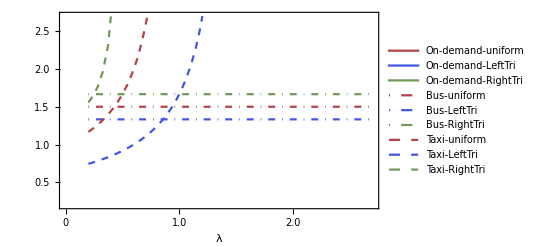

```mathematica
plotLow = Plot[{EwaitUnif[λ], EwaitTri1[λ], EwaitTri2[λ], EWaitbusUnif[λ],EWaitbusTri1[λ],EWaitbusTri2[λ],EwaitTaxiLineUnifNew[λ], EwaitTaxiLineTri1[λ], EwaitTaxiLineTri2[λ]},{λ,0.2,2.7}, 
PlotPoints->30, MaxRecursion->1, 
Frame->{{True,False},{True,False}},PlotStyle->{
{ColorData["ThermometerColors",0.9],Thick},{Thick,ColorData["ThermometerColors",0.1]},{Thick,ColorData["WatermelonColors",0.3]},
{ColorData["ThermometerColors",0.9],DotDashed},{ColorData["ThermometerColors",0.1],DotDashed},{ColorData["WatermelonColors",0.3],DotDashed},
{ColorData["ThermometerColors",0.9],Dashed},{Dashed,ColorData["ThermometerColors",0.1]},{Dashed,ColorData["WatermelonColors",0.3]}
},
PlotRange->{0.2,2.7},PlotLegends->{"On-demand-uniform", "On-demand-LeftTri", "On-demand-RightTri", "Bus-uniform", "Bus-LeftTri", "Bus-RightTri","Taxi-uniform", "Taxi-LeftTri", "Taxi-RightTri"}, 
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["",16,Bold]},FrameTicks->All]
```

#### High λ Range

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$2549645].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$2562223].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First::normal will be suppressed during this calculation.

FindSequenceFunction::list: List expected at position 1 in FindSequenceFunction[First[$Failed],RandomProcesses`MarkovChainDump`k$2574807].

General::stop: Further output of FindSequenceFunction::list will be suppressed during this calculation.

Table::iterb: Iterator {i,0,-1+a} does not have appropriate bounds.

Table::iterb: Iterator {i,a,4} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator If[j<QueueCap51,PijsmallTri1[i,j,0.200338],1-Total[Table[PijsmallTri1[i,jj,0.200338],{jj,0,QueueCap51-1}]]] at position 4 does not evaluate to a real numeric value.

DiscreteMarkovProcess::bprm: The parameters of distribution DiscreteMarkovProcess[2,Re[Table[If[j==a,1,0],{i,0,-1+a},{j,0,QueueCap51},If[j<QueueCap51,PijsmallTri1[i,j,0.200338],1-Total[Table[«2»]]],{i,a,4},{j,0,QueueCap51}]]] are not valid. Use DistributionParameterAssumptions to obtain the parameter assumptions.

General::stop: Further output of DiscreteMarkovProcess::bprm will be suppressed during this calculation.

Table::nliter: Non-list iterator If[j<QueueCap51,PijsmallTri1[i,j,0.200338],1-Total[Table[PijsmallTri1[i,jj,0.200338],{jj,0,QueueCap51-1}]]] at position 4 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

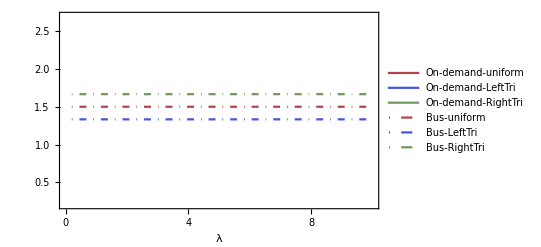

```mathematica
plotHigh = Plot[{EwaitUnif[λ], EwaitTri1[λ], EwaitTri2[λ],  EWaitbusUnif[λ],EWaitbusTri1[λ],EWaitbusTri2[λ]},{λ,0.2,10}, 
PlotPoints->30, MaxRecursion->1, 
Frame->{{True,False},{True,False}},PlotStyle->{
{ColorData["ThermometerColors",0.9],Thick},{Thick,ColorData["ThermometerColors",0.1]},{Thick,ColorData["WatermelonColors",0.3]},
{ColorData["ThermometerColors",0.9],DotDashed},{ColorData["ThermometerColors",0.1],DotDashed},{ColorData["WatermelonColors",0.3],DotDashed},
{ColorData["ThermometerColors",0.9],Dashed},{Dashed,ColorData["ThermometerColors",0.1]},{Dashed,ColorData["WatermelonColors",0.3]}
},
PlotRange->{0.2,2.7},PlotLegends->{"On-demand-uniform", "On-demand-LeftTri", "On-demand-RightTri", "Bus-uniform", "Bus-LeftTri", "Bus-RightTri"}, 
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["",16,Bold]},FrameTicks->All]
```

### Exporting Options

Here the user has to define their desired location for the export of the graphs.
  Tip : Copying and pasting the file directory in Mathematica automatically replaces "\" with " \\ ", which is the required syntax by Mathematica.

Must be changed before the run!

```mathematica
Route=NotebookDirectory[];
```

```mathematica
Export[ToString[Route]<>"low.pdf", plotLow]
Export[ToString[Route]<>"high.pdf", plotHigh]
```

Export::nodir: Directory C:\Users\bzk0054\Desktop\Auburn University\ does not exist.

Export::noopen: Cannot open C:\Users\bzk0054\Desktop\Auburn University\low.pdf.

$Failed

Export::nodir: Directory C:\Users\bzk0054\Desktop\Auburn University\ does not exist.

Export::noopen: Cannot open C:\Users\bzk0054\Desktop\Auburn University\high.pdf.

$Failed

## Plotting - Fig 2

#### Idling Rate

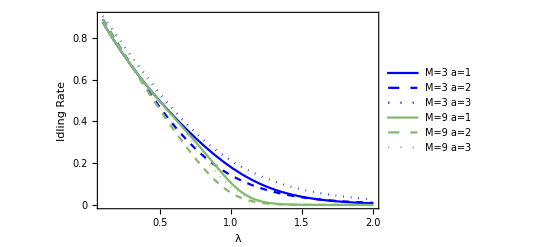

```mathematica
pIdle2= Plot[{{ EidleRev1[λ,1,3],EidleRev1[λ,2,3], EidleRev1[λ,3,3],EidleRev1[λ,1,9],EidleRev1[λ,2,9], EidleRev1[λ,3,9]}},{λ,0.1,2}, 
PlotPoints->30, MaxRecursion->1, PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotStyle->{{Thick,Blue},{Thick,Dashed,Blue},{Thick,Dotted,Blue},{Thick,ColorData["Rainbow",0.5]},{Thick,Dashed,ColorData["Rainbow",0.5]},{Thick,Dotted,ColorData["Rainbow",0.5]}},PlotLegends->Placed[{"M=3 a=1", "M=3 a=2", "M=3 a=3", "M=9 a=1", "M=9 a=2","M=9 a=3"},Above], 
Axes->False,
Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Idling Rate",16,Bold]},FrameTicks->All]
```

#### Number of Passengers

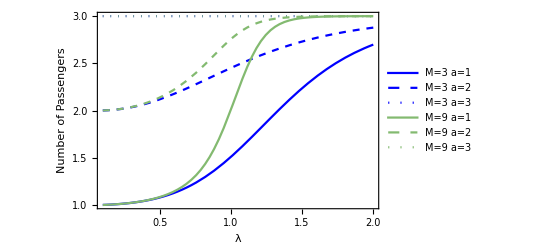

```mathematica
pNum2= Plot[{{EnumRev1[λ, 1, 3],EnumRev1[λ, 2, 3],  EnumRev1[λ, 3, 3], EnumRev1[λ, 1, 9],EnumRev1[λ, 2, 9],  EnumRev1[λ, 3, 9]}},{λ,0.1,2}, 
PlotPoints->30, MaxRecursion->1, PlotRange->Full,
Frame->{{True,False},{True,False}},PlotStyle->{{Thick,Blue},{Thick,Dashed,Blue},{Thick,Dotted,Blue},{Thick,ColorData["Rainbow",0.5]},{Thick,Dashed,ColorData["Rainbow",0.5]},{Thick,Dotted,ColorData["Rainbow",0.5]}},
PlotLegends->Placed[{"M=3 a=1", "M=3 a=2", "M=3 a=3", "M=9 a=1", "M=9 a=2","M=9 a=3"},Above], 
Axes->False,
Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Number of Passengers",16,Bold]},FrameTicks->All]
```

#### Admission Rate

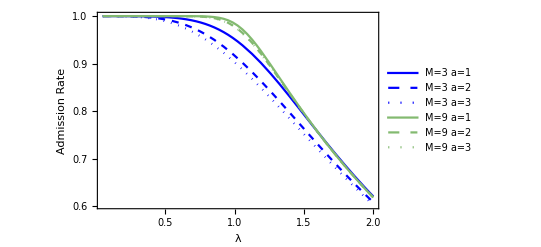

```mathematica
pAdmit2= Plot[{{AdmitRev1[λ,1,3],AdmitRev1[λ,2,3], AdmitRev1[λ,3,3], AdmitRev1[λ,1,9],AdmitRev1[λ,2,9],AdmitRev1[λ,3,9]}},{λ,0.05,2}, 
PlotPoints->30, MaxRecursion->1, PlotRange->Full,
Frame->{{True,False},{True,False}},
PlotStyle->{{Thick,Blue},{Thick,Dashed,Blue},{Thick,Dotted,Blue},{Thick,ColorData["Rainbow",0.5]},{Thick,Dashed,ColorData["Rainbow",0.5]},{Thick,Dotted,ColorData["Rainbow",0.5]}},
PlotLegends->Placed[{"M=3 a=1", "M=3 a=2", "M=3 a=3", "M=9 a=1", "M=9 a=2","M=9 a=3"}, Above], 
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["λ",16,Bold],Style["Admission Rate",16,Bold]},FrameTicks->All]
```

#### Admission Rate (zoomed in)

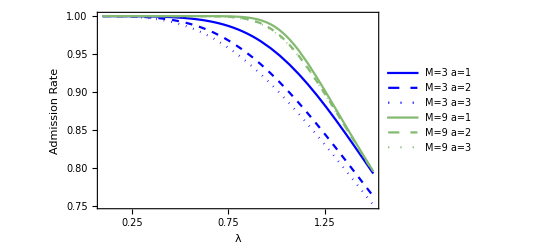

```mathematica
pAdmitZoomed2= Plot[{ {AdmitRev1[λ, 1, 3],AdmitRev1[λ, 2, 3], AdmitRev1[λ, 3, 3], AdmitRev1[λ, 1, 9],AdmitRev1[λ, 2, 9],AdmitRev1[λ, 3, 9]}},{λ,0.5,1.5}, 
PlotPoints->30, MaxRecursion->1, PlotRange->Full,
Frame->{{True,False},{True,False}},PlotStyle->{{Thick,Blue},{Thick,Dashed,Blue},{Thick,Dotted,Blue},{Thick,ColorData["Rainbow",0.5]},{Thick,Dashed,ColorData["Rainbow",0.5]},{Thick,Dotted,ColorData["Rainbow",0.5]}},
PlotLegends->Placed[{"M=3 a=1", "M=3 a=2", "M=3 a=3", "M=9 a=1", "M=9 a=2","M=9 a=3"},Above], 
Axes->False,
Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Admission Rate",16,Bold]},FrameTicks->All]
```

#### Exporting Options

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_2a_2_idle.pdf", pIdle2];
Export[ToString[NotebookDirectory[]]<>"fig_2b_2_num.pdf", pNum2];
Export[ToString[NotebookDirectory[]]<>"fig_2c_2_admit.pdf", pAdmit2];
Export[ToString[NotebookDirectory[]]<>"fig_2d_2_admitZoom.pdf", pAdmitZoomed2];
```

## Plotting - Fig 3 & 4

The structure is as follows, first we plot CTMC models’ measures, then partitioning models’ and finally we put them all on the same plot to compare.

We do the same for a scaling λs, to see how well the model adjust to increasing demand levels.

### Constant λs (Fig 3)

In this subsection, λs are the same for all models and for all their extensions.

#### Idling Rate

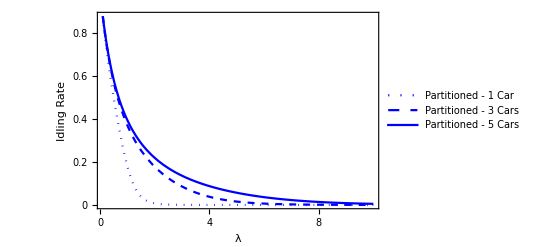

```mathematica
partUnsIdle=Plot[{EidlePart[λ,1],EidlePart[λ,3],EidlePart[λ,5]},{λ,0.1,10},PlotRange->Full,PlotStyle->{{Blue,Dotted,Thick},{Blue,Dashed,Thick},{Blue,Thick}},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Idling Rate",16,Bold]},FrameTicks->All, PlotLegends->Placed[{"Partitioned m=1","Partitioned m=3","Partitioned m=5"},Above]]
```

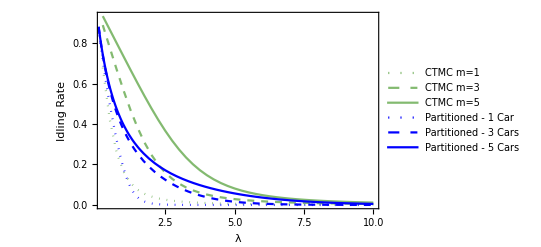

```mathematica
partCUnsIdle=Show[ListLinePlot[{
Transpose[{Lambdas,Sdist1Car3Kap1tH[[1]]}],
Transpose[{Lambdas,Total[Sdist3Car3Kap1tH[[Indices3Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist5Car3Kap1tH[[Indices5Cars3Kap1tH0num]]]}]
},
PlotRange->Full, PlotLegends->Placed[{"CTMC m=1",  "CTMC m=3","CTMC m=5"},{0.75,0.75}],Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Idling Rate",16,Bold]},FrameTicks->All,PlotStyle->{{ColorData["Rainbow",0.5],Dotted,Thick},{ColorData["Rainbow",0.5],Dashed,Thick},{ColorData["Rainbow",0.5],Thick}}],partUnsIdle]
```

#### Number of Passengers

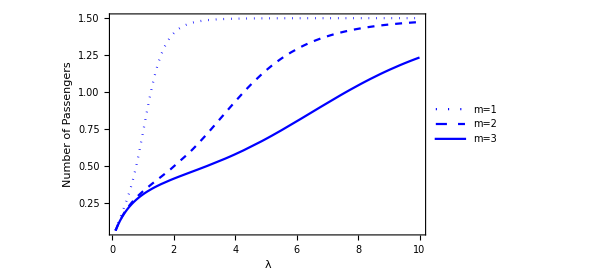

```mathematica
partUnsNum=Plot[{{EutilPart[λ,1],EutilPart[λ,3],EutilPart[λ,5]}},{λ,0.1,10},PlotPoints->3,PlotRange->Full,PlotStyle->{{Blue,Dotted,Thick},{Blue,Dashed,Thick},{Blue,Thick}},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Number of Passengers",16,Bold]},FrameTicks->All,PlotLegends->Placed[{"m=1","m=2","m=3"}, Above],ImageSize->450]
```

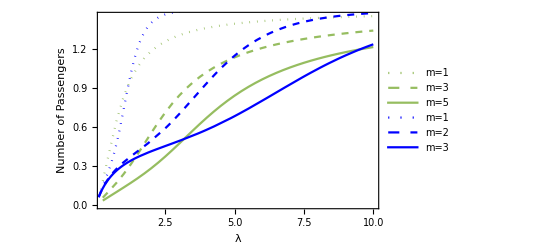

```mathematica
partCUnsNum=Show[ListLinePlot[{
Transpose[{Lambdas,(Total[Sdist1Car3Kap1tH[[Indices1Cars3Kap1tH1num]]]+2*Total[Sdist1Car3Kap1tH[[Indices1Cars3Kap1tH2num]]]+3*Total[Sdist1Car3Kap1tH[[Indices1Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist3Car3Kap1tH[[Indices3Cars3Kap1tH1num]]]+2*Total[Sdist3Car3Kap1tH[[Indices3Cars3Kap1tH2num]]]+3*Total[Sdist3Car3Kap1tH[[Indices3Cars3Kap1tH3num]]])/2}],Transpose[{Lambdas,(Total[Sdist5Car3Kap1tH[[Indices5Cars3Kap1tH1num]]]+2*Total[Sdist5Car3Kap1tH[[Indices5Cars3Kap1tH2num]]]+3*Total[Sdist5Car3Kap1tH[[Indices5Cars3Kap1tH3num]]])/2}]
},
PlotRange->Full, PlotLegends->Placed[{"m=1",  "m=3","m=5"},Above],Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Number of Passengers",16,Bold]},FrameTicks->All,PlotStyle->{{ColorData["Rainbow",0.55],Dotted,Thick},{ColorData["Rainbow",0.55],Dashed,Thick},{ColorData["Rainbow",0.55],Thick}}],partUnsNum
]
```

#### Admission Rate

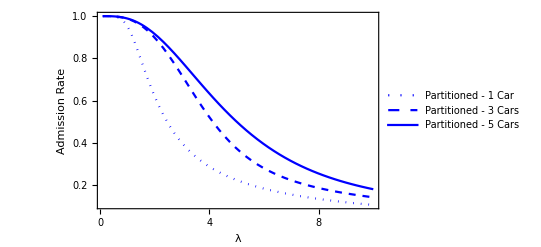

```mathematica
partUnsadmit=Plot[{EadmitPart[λ,1],EadmitPart[λ,3], EadmitPart[λ, 5]},{λ,0.1,10},PlotRange->Full,PlotStyle->{{Blue,Dotted,Thick},{Blue,Dashed,Thick},{Blue,Thick}},Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Admission Rate",16,Bold]},FrameTicks->All,PlotLegends->Placed[{ "Partitioned - 1 Car","Partitioned - 3 Cars","Partitioned - 5 Cars"}, Above]]
```

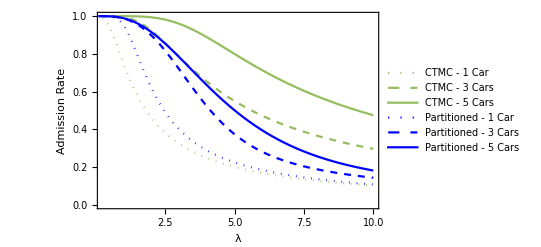

```mathematica
partCUnsAdmit=Show[ListLinePlot[
{Transpose[{Lambdas,1-Total[Sdist1Car3Kap1tH[[Indices1Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist3Car3Kap1tH[[Indices3Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist5Car3Kap1tH[[Indices5Cars3Kap1tH3wait]]]}]
},
PlotRange->Full, PlotLegends->Placed[{"CTMC - 1 Car",  "CTMC - 3 Cars","CTMC - 5 Cars"},Above],Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Admission Rate",16,Bold]},FrameTicks->All,PlotStyle->{{ColorData["Rainbow",0.55],Dotted,Thick},{ColorData["Rainbow",0.55],Dashed,Thick},{ColorData["Rainbow",0.55],Thick}}]
,partUnsadmit]
```

#### Exporting Options

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_3a_idle.pdf",partCUnsIdle];
Export[ToString[NotebookDirectory[]]<>"fig_3b_num.pdf",partCUnsNum];
Export[ToString[NotebookDirectory[]]<>"fig_3c_admit.pdf",partCUnsAdmit];
```

### CTMC Model, Scaling λs (Fig 4-a-c-e)

In this subsection, λs are scaling for CTMC model. We need to import the stationary distributions generated using our Python code.

#### Imports

```mathematica
Sdist1Car3Kap1tHScaled=Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_1Cars_3DepotCap_1Threshold_1scaled.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist2Car3Kap1tHScaled =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_2Cars_3DepotCap_1Threshold_2scaled.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist3Car3Kap1tHScaled =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_3Cars_3DepotCap_1Threshold_3scaled.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist4Car3Kap1tHScaled =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_4Cars_3DepotCap_1Threshold_4scaled.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist5Car3Kap1tHScaled =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_5Cars_3DepotCap_1Threshold_5scaled.csv"}],"Data","SkipLines"-> {1,1}]];
Sdist6Car3Kap1tHScaled =Transpose[Import[FileNameJoin[{NotebookDirectory[],"stuff","sDistList_6Cars_3DepotCap_1Threshold_6scaled.csv"}],"Data","SkipLines"-> {1,1}]];
```

#### Idling Rate

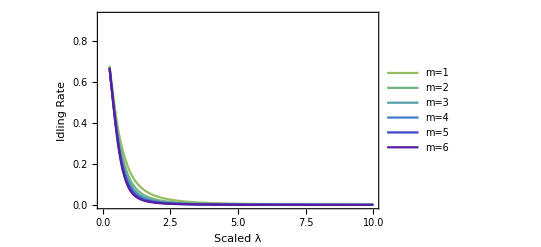

```mathematica
idleScaCTMC=ListLinePlot[{
Transpose[{Lambdas,Sdist1Car3Kap1tHScaled[[1]]}],
Transpose[{Lambdas,Total[Sdist2Car3Kap1tHScaled[[Indices2Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist3Car3Kap1tHScaled[[Indices3Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist4Car3Kap1tHScaled[[Indices4Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist5Car3Kap1tHScaled[[Indices5Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist6Car3Kap1tHScaled[[Indices6Cars3Kap1tH0num]]]}]
},PlotRange->{Automatic,{0,0.92}}, PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above],PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Idling Rate",16,Bold]},
FrameTicks->All,InterpolationOrder->3]
```

#### Number of Passengers

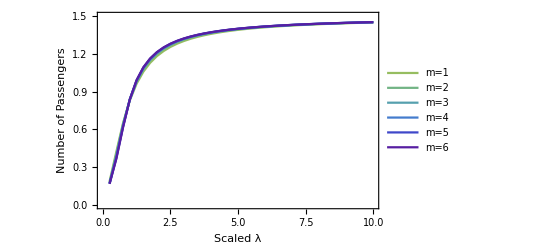

```mathematica
numScaCTMC=ListLinePlot[
{Transpose[{Lambdas,(Total[Sdist1Car3Kap1tHScaled[[Indices1Cars3Kap1tH1num]]]+2*Total[Sdist1Car3Kap1tHScaled[[Indices1Cars3Kap1tH2num]]]+3*Total[Sdist1Car3Kap1tHScaled[[Indices1Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist2Car3Kap1tHScaled[[Indices2Cars3Kap1tH1num]]]+2*Total[Sdist2Car3Kap1tHScaled[[Indices2Cars3Kap1tH2num]]]+3*Total[Sdist2Car3Kap1tHScaled[[Indices2Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist3Car3Kap1tHScaled[[Indices3Cars3Kap1tH1num]]]+2*Total[Sdist3Car3Kap1tHScaled[[Indices3Cars3Kap1tH2num]]]+3*Total[Sdist3Car3Kap1tHScaled[[Indices3Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist4Car3Kap1tHScaled[[Indices4Cars3Kap1tH1num]]]+2*Total[Sdist4Car3Kap1tHScaled[[Indices4Cars3Kap1tH2num]]]+3*Total[Sdist4Car3Kap1tHScaled[[Indices4Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist5Car3Kap1tHScaled[[Indices5Cars3Kap1tH1num]]]+2*Total[Sdist5Car3Kap1tHScaled[[Indices5Cars3Kap1tH2num]]]+3*Total[Sdist5Car3Kap1tHScaled[[Indices5Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist6Car3Kap1tHScaled[[Indices6Cars3Kap1tH1num]]]+2*Total[Sdist6Car3Kap1tHScaled[[Indices6Cars3Kap1tH2num]]]+3*Total[Sdist6Car3Kap1tHScaled[[Indices6Cars3Kap1tH3num]]])/2}]
},
PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},PlotRange->{Automatic,{0,1.5}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Number of Passengers",16,Bold]},FrameTicks->All,PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above]]
```

#### Admission Rate

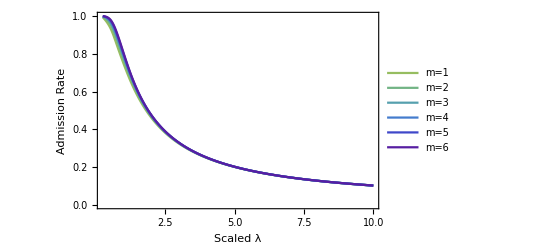

```mathematica
admitScaCTMC=
ListLinePlot[{Transpose[{Lambdas,1-Total[Sdist1Car3Kap1tHScaled[[Indices1Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist2Car3Kap1tHScaled[[Indices2Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist3Car3Kap1tHScaled[[Indices3Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist4Car3Kap1tHScaled[[Indices4Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist5Car3Kap1tHScaled[[Indices5Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Total[Sdist6Car3Kap1tHScaled[[Indices6Cars3Kap1tH3wait]]]}]},
PlotRange->Full,PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above],PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Admission Rate",16,Bold]},
FrameTicks->All,InterpolationOrder->3]
```

#### Exporting Options

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_4a_idle.pdf",idleScaCTMC];
Export[ToString[NotebookDirectory[]]<>"fig_4c_num.pdf",numScaCTMC];
Export[ToString[NotebookDirectory[]]<>"fig_4e_admit.pdf",admitScaCTMC];
```

### Partitioned Model, Scaling λs (Fig 4-b-d-f)

In this subsection, λs are scaling for the partitioned model. This allows us to see how well the models adjust to increasing demand. 
Our current scaling constant is equal to mλ, where m represents the number of cars available.

#### Idling Rate

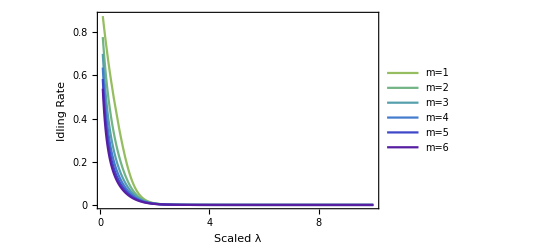

```mathematica
partScaIdleAll2=Plot[{EidlePart[λ,1],EidlePart[2λ,2],EidlePart[3λ,3],EidlePart[4λ,4],EidlePart[5λ,5],EidlePart[6λ,6]},{λ,0.1,10},PlotRange->Full,PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Idling Rate",16,Bold]},
FrameTicks->All, PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above]]
```

#### Number of Passengers

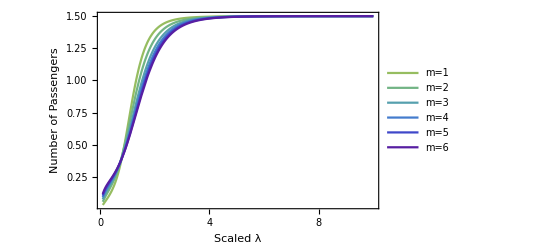

```mathematica
partScaNumAll2=Plot[{EutilPart[λ,1],EutilPart[2λ,2],EutilPart[3λ,3],EutilPart[4λ,4],EutilPart[5λ,5], EutilPart[6λ, 6]},{λ,0.1,10},PlotRange->Full,PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Number of Passengers",16,Bold]},FrameTicks->All,PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above]]
```

#### Admission Rate

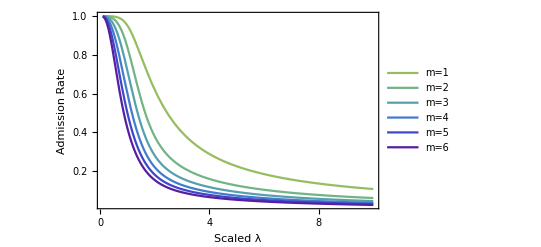

```mathematica
partScaAdmitAll2=Plot[{EadmitPart[λ,1],EadmitPart[2λ,2],EadmitPart[3λ,3],EadmitPart[4λ,4],EadmitPart[5λ,5], EadmitPart[6λ,6]},{λ,0.1,10},PlotRange->Full,PlotStyle->{{ColorData["Rainbow",0.55],Thick},{ColorData["Rainbow",0.45],Thick},{ColorData["Rainbow",0.35],Thick},{ColorData["Rainbow",0.25],Thick},{ColorData["Rainbow",0.15],Thick},{ColorData["Rainbow",0.05],Thick}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Scaled λ",16,Bold],Style["Admission Rate",16,Bold]},
FrameTicks->All,
PlotLegends->Placed[{"m=1","m=2","m=3","m=4","m=5","m=6"}, Above]]
```

#### Exporting Options

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_4b_idle.pdf",partScaIdleAll2];
```

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_4d_num.pdf",partScaNumAll2];
```

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_4f_admit.pdf",partScaAdmitAll2];
```

## Plotting - Fig 5

### Idling Rate

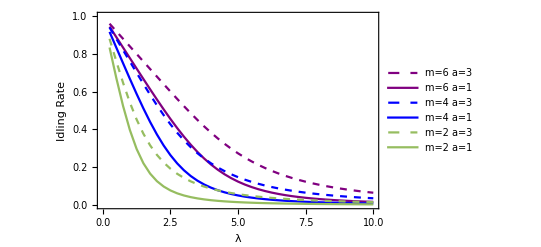

```mathematica
idletHalt=ListLinePlot[{
Transpose[{Lambdas,Total[Sdist6Car3Kap3tH[[Indices6Cars3Kap3tH0num]]]}],
Transpose[{Lambdas,Total[Sdist6Car3Kap1tH[[Indices6Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist4Car3Kap3tH[[Indices4Cars3Kap3tH0num]]]}],
Transpose[{Lambdas,Total[Sdist4Car3Kap1tH[[Indices4Cars3Kap1tH0num]]]}],
Transpose[{Lambdas,Total[Sdist2Car3Kap3tH[[Indices2Cars3Kap3tH0num]]]}],
Transpose[{Lambdas,Total[Sdist2Car3Kap1tH[[Indices2Cars3Kap1tH0num]]]}]
},
PlotRange->{Automatic,{0,1}}, PlotLegends->Placed[{"m=6 a=3","m=6 a=1","m=4 a=3","m=4 a=1","m=2 a=3","m=2 a=1"},Above],PlotStyle->{{Thick,Dashed,Purple},{Thick,Purple},{Thick,Dashed,Blue},{Thick,Blue},{Thick,Dashed,ColorData["Rainbow",0.55]},{Thick,ColorData["Rainbow",0.55]}},Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Idling Rate",16,Bold]}]
```

### Number of Passengers

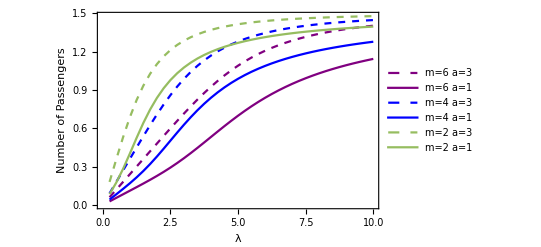

```mathematica
numtHalt=ListLinePlot[{
Transpose[{Lambdas,(3*Total[Sdist6Car3Kap3tH[[Indices6Cars3Kap3tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist6Car3Kap1tH[[Indices6Cars3Kap1tH1num]]]+2*Total[Sdist6Car3Kap1tH[[Indices6Cars3Kap1tH2num]]]+3*Total[Sdist6Car3Kap1tH[[Indices6Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(3*Total[Sdist4Car3Kap3tH[[Indices4Cars3Kap3tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist4Car3Kap1tH[[Indices4Cars3Kap1tH1num]]]+2*Total[Sdist4Car3Kap1tH[[Indices4Cars3Kap1tH2num]]]+3*Total[Sdist4Car3Kap1tH[[Indices4Cars3Kap1tH3num]]])/2}],
Transpose[{Lambdas,(3*Total[Sdist2Car3Kap3tH[[Indices2Cars3Kap3tH3num]]])/2}],
Transpose[{Lambdas,(Total[Sdist2Car3Kap1tH[[Indices2Cars3Kap1tH1num]]]+2*Total[Sdist2Car3Kap1tH[[Indices2Cars3Kap1tH2num]]]+3*Total[Sdist2Car3Kap1tH[[Indices2Cars3Kap1tH3num]]])/2}]
},
PlotRange->{Automatic,Automatic},PlotLegends->Placed[{"m=6 a=3","m=6 a=1","m=4 a=3","m=4 a=1","m=2 a=3","m=2 a=1"},Above],PlotStyle->{{Thick,Dashed,Purple},{Thick,Purple},{Thick,Dashed,Blue},{Thick,Blue},{Thick,Dashed,ColorData["Rainbow",0.55]},{Thick,ColorData["Rainbow",0.55]}},Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Number of Passengers",16,Bold]}]
```

### Admission Rate

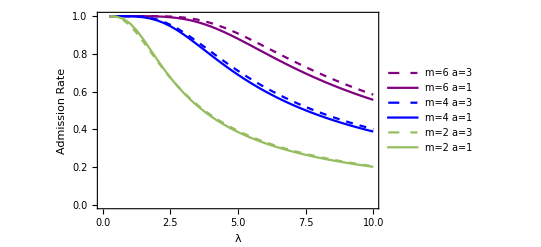

```mathematica
admittHalt=ListLinePlot[
{
Transpose[{Lambdas,1-Sdist6Car3Kap3tH[[193]]}],
Transpose[{Lambdas,1-Total[Sdist6Car3Kap1tH[[Indices6Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Sdist4Car3Kap3tH[[49]]}],
Transpose[{Lambdas,1-Total[Sdist4Car3Kap1tH[[Indices4Cars3Kap1tH3wait]]]}],
Transpose[{Lambdas,1-Sdist2Car3Kap3tH[[13]]}],
Transpose[{Lambdas,1-Total[Sdist2Car3Kap1tH[[Indices2Cars3Kap1tH3wait]]]}]
},
PlotRange->{Automatic,Automatic},PlotLegends->Placed[{"m=6 a=3","m=6 a=1","m=4 a=3","m=4 a=1","m=2 a=3","m=2 a=1"},Above],PlotStyle->{{Thick,Dashed,Purple},{Thick,Purple},{Thick,Dashed,Blue},{Thick,Blue},{Thick,Dashed,ColorData["Rainbow",0.55]},{Thick,ColorData["Rainbow",0.55]}},Frame->{{True,False},{True,False}},FrameLabel->{Style["λ",16,Bold],Style["Admission Rate",16,Bold]}]
```

### Exporting Options

```mathematica
Export[ToString[NotebookDirectory[]]<>"fig_5_idle_alt.pdf",idletHalt];
Export[ToString[NotebookDirectory[]]<>"fig_5_num_alt.pdf",numtHalt];
Export[ToString[NotebookDirectory[]]<>"fig_5_admit_alt.pdf",admittHalt];
```

## References

Vinel, Alexander, and Daniel F. Silva. “Probability distribution of the length of the shortest tour between a few random points: a simulation study.” 2018 Winter Simulation Conference (WSC). IEEE, 2018.

Ciardo, Gianfranco. “Tools for formulating Markov models.” Computational Probability. Springer, Boston, MA, 2000. 11-41.